```mathematica
et[n_,k_]:=et[n,k]=Sum[et[j,k-1] et[n/j,1],{j,Divisors[n]}];et[n_,1]:=(-1)^(n+1);et[n_,0]:=0;et[1,0]:=1
et2[n_,k_]:=et2[n,k]=Sum[(-1)^j Binomial[k,j] et[n,k-j],{j,0,k}]
ET2[n_,k_] := ET2[n,k]=Sum[ et2[j,k],{j,2,n}]
lin[n_]:=Sum[(-1)^(k+1)/k et2[n,k],{k,1,Log[2,n]}]
Lin[n_]:=Lin[n]=Sum[(-1)^(k+1)/k ET2[n,k],{k,1,Log[2,n]}]
LAdd[n_] := Sum[ 2^k/k,{k,1,Log[2,n]}]
Table[ {n,et2[n,1],et2[n,2],et2[n,3],et2[n,4], lin[n]},{n,1,100}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0
2 | -1 | 0 | 0 | 0 | -1
3 | 1 | 0 | 0 | 0 | 1
4 | -1 | 1 | 0 | 0 | -3/2
5 | 1 | 0 | 0 | 0 | 1
6 | -1 | -2 | 0 | 0 | 0
7 | 1 | 0 | 0 | 0 | 1
8 | -1 | 2 | -1 | 0 | -7/3
9 | 1 | 1 | 0 | 0 | 1/2
10 | -1 | -2 | 0 | 0 | 0
11 | 1 | 0 | 0 | 0 | 1
12 | -1 | 0 | 3 | 0 | 0
13 | 1 | 0 | 0 | 0 | 1
14 | -1 | -2 | 0 | 0 | 0
15 | 1 | 2 | 0 | 0 | 0
16 | -1 | 3 | -3 | 1 | -15/4
17 | 1 | 0 | 0 | 0 | 1
18 | -1 | -4 | -3 | 0 | 0
19 | 1 | 0 | 0 | 0 | 1
20 | -1 | 0 | 3 | 0 | 0
21 | 1 | 2 | 0 | 0 | 0
22 | -1 | -2 | 0 | 0 | 0
23 | 1 | 0 | 0 | 0 | 1
24 | -1 | 2 | 3 | -4 | 0
25 | 1 | 1 | 0 | 0 | 1/2
26 | -1 | -2 | 0 | 0 | 0
27 | 1 | 2 | 1 | 0 | 1/3
28 | -1 | 0 | 3 | 0 | 0
29 | 1 | 0 | 0 | 0 | 1
30 | -1 | -6 | -6 | 0 | 0
31 | 1 | 0 | 0 | 0 | 1
32 | -1 | 4 | -6 | 4 | -31/5
33 | 1 | 2 | 0 | 0 | 0
34 | -1 | -2 | 0 | 0 | 0
35 | 1 | 2 | 0 | 0 | 0
36 | -1 | -1 | 6 | 6 | 0
37 | 1 | 0 | 0 | 0 | 1
38 | -1 | -2 | 0 | 0 | 0
39 | 1 | 2 | 0 | 0 | 0
40 | -1 | 2 | 3 | -4 | 0
41 | 1 | 0 | 0 | 0 | 1
42 | -1 | -6 | -6 | 0 | 0
43 | 1 | 0 | 0 | 0 | 1
44 | -1 | 0 | 3 | 0 | 0
45 | 1 | 4 | 3 | 0 | 0
46 | -1 | -2 | 0 | 0 | 0
47 | 1 | 0 | 0 | 0 | 1
48 | -1 | 4 | 0 | -8 | 0
49 | 1 | 1 | 0 | 0 | 1/2
50 | -1 | -4 | -3 | 0 | 0
51 | 1 | 2 | 0 | 0 | 0
52 | -1 | 0 | 3 | 0 | 0
53 | 1 | 0 | 0 | 0 | 1
54 | -1 | -6 | -9 | -4 | 0
55 | 1 | 2 | 0 | 0 | 0
56 | -1 | 2 | 3 | -4 | 0
57 | 1 | 2 | 0 | 0 | 0
58 | -1 | -2 | 0 | 0 | 0
59 | 1 | 0 | 0 | 0 | 1
60 | -1 | -2 | 9 | 12 | 0
61 | 1 | 0 | 0 | 0 | 1
62 | -1 | -2 | 0 | 0 | 0
63 | 1 | 4 | 3 | 0 | 0
64 | -1 | 5 | -10 | 10 | -21/2
65 | 1 | 2 | 0 | 0 | 0
66 | -1 | -6 | -6 | 0 | 0
67 | 1 | 0 | 0 | 0 | 1
68 | -1 | 0 | 3 | 0 | 0
69 | 1 | 2 | 0 | 0 | 0
70 | -1 | -6 | -6 | 0 | 0
71 | 1 | 0 | 0 | 0 | 1
72 | -1 | 2 | 9 | -4 | 0
73 | 1 | 0 | 0 | 0 | 1
74 | -1 | -2 | 0 | 0 | 0
75 | 1 | 4 | 3 | 0 | 0
76 | -1 | 0 | 3 | 0 | 0
77 | 1 | 2 | 0 | 0 | 0
78 | -1 | -6 | -6 | 0 | 0
79 | 1 | 0 | 0 | 0 | 1
80 | -1 | 4 | 0 | -8 | 0
81 | 1 | 3 | 3 | 1 | 1/4
82 | -1 | -2 | 0 | 0 | 0
83 | 1 | 0 | 0 | 0 | 1
84 | -1 | -2 | 9 | 12 | 0
85 | 1 | 2 | 0 | 0 | 0
86 | -1 | -2 | 0 | 0 | 0
87 | 1 | 2 | 0 | 0 | 0
88 | -1 | 2 | 3 | -4 | 0
89 | 1 | 0 | 0 | 0 | 1
90 | -1 | -10 | -21 | -12 | 0
91 | 1 | 2 | 0 | 0 | 0
92 | -1 | 0 | 3 | 0 | 0
93 | 1 | 2 | 0 | 0 | 0
94 | -1 | -2 | 0 | 0 | 0
95 | 1 | 2 | 0 | 0 | 0
96 | -1 | 6 | -6 | -8 | 0
97 | 1 | 0 | 0 | 0 | 1
98 | -1 | -4 | -3 | 0 | 0
99 | 1 | 4 | 3 | 0 | 0
100 | -1 | -1 | 6 | 6 | 0

```mathematica
Table[ {n,et2[n,1],et2[n,2],et2[n,3],et2[n,4], lin[n]},{n,1,100}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0
2 | -1 | 0 | 0 | 0 | -1
3 | 1 | 0 | 0 | 0 | 1
4 | -1 | 1 | 0 | 0 | -3/2
5 | 1 | 0 | 0 | 0 | 1
6 | -1 | -2 | 0 | 0 | 0
7 | 1 | 0 | 0 | 0 | 1
8 | -1 | 2 | -1 | 0 | -7/3
9 | 1 | 1 | 0 | 0 | 1/2
10 | -1 | -2 | 0 | 0 | 0
11 | 1 | 0 | 0 | 0 | 1
12 | -1 | 0 | 3 | 0 | 0
13 | 1 | 0 | 0 | 0 | 1
14 | -1 | -2 | 0 | 0 | 0
15 | 1 | 2 | 0 | 0 | 0
16 | -1 | 3 | -3 | 1 | -15/4
17 | 1 | 0 | 0 | 0 | 1
18 | -1 | -4 | -3 | 0 | 0
19 | 1 | 0 | 0 | 0 | 1
20 | -1 | 0 | 3 | 0 | 0
21 | 1 | 2 | 0 | 0 | 0
22 | -1 | -2 | 0 | 0 | 0
23 | 1 | 0 | 0 | 0 | 1
24 | -1 | 2 | 3 | -4 | 0
25 | 1 | 1 | 0 | 0 | 1/2
26 | -1 | -2 | 0 | 0 | 0
27 | 1 | 2 | 1 | 0 | 1/3
28 | -1 | 0 | 3 | 0 | 0
29 | 1 | 0 | 0 | 0 | 1
30 | -1 | -6 | -6 | 0 | 0
31 | 1 | 0 | 0 | 0 | 1
32 | -1 | 4 | -6 | 4 | -31/5
33 | 1 | 2 | 0 | 0 | 0
34 | -1 | -2 | 0 | 0 | 0
35 | 1 | 2 | 0 | 0 | 0
36 | -1 | -1 | 6 | 6 | 0
37 | 1 | 0 | 0 | 0 | 1
38 | -1 | -2 | 0 | 0 | 0
39 | 1 | 2 | 0 | 0 | 0
40 | -1 | 2 | 3 | -4 | 0
41 | 1 | 0 | 0 | 0 | 1
42 | -1 | -6 | -6 | 0 | 0
43 | 1 | 0 | 0 | 0 | 1
44 | -1 | 0 | 3 | 0 | 0
45 | 1 | 4 | 3 | 0 | 0
46 | -1 | -2 | 0 | 0 | 0
47 | 1 | 0 | 0 | 0 | 1
48 | -1 | 4 | 0 | -8 | 0
49 | 1 | 1 | 0 | 0 | 1/2
50 | -1 | -4 | -3 | 0 | 0
51 | 1 | 2 | 0 | 0 | 0
52 | -1 | 0 | 3 | 0 | 0
53 | 1 | 0 | 0 | 0 | 1
54 | -1 | -6 | -9 | -4 | 0
55 | 1 | 2 | 0 | 0 | 0
56 | -1 | 2 | 3 | -4 | 0
57 | 1 | 2 | 0 | 0 | 0
58 | -1 | -2 | 0 | 0 | 0
59 | 1 | 0 | 0 | 0 | 1
60 | -1 | -2 | 9 | 12 | 0
61 | 1 | 0 | 0 | 0 | 1
62 | -1 | -2 | 0 | 0 | 0
63 | 1 | 4 | 3 | 0 | 0
64 | -1 | 5 | -10 | 10 | -21/2
65 | 1 | 2 | 0 | 0 | 0
66 | -1 | -6 | -6 | 0 | 0
67 | 1 | 0 | 0 | 0 | 1
68 | -1 | 0 | 3 | 0 | 0
69 | 1 | 2 | 0 | 0 | 0
70 | -1 | -6 | -6 | 0 | 0
71 | 1 | 0 | 0 | 0 | 1
72 | -1 | 2 | 9 | -4 | 0
73 | 1 | 0 | 0 | 0 | 1
74 | -1 | -2 | 0 | 0 | 0
75 | 1 | 4 | 3 | 0 | 0
76 | -1 | 0 | 3 | 0 | 0
77 | 1 | 2 | 0 | 0 | 0
78 | -1 | -6 | -6 | 0 | 0
79 | 1 | 0 | 0 | 0 | 1
80 | -1 | 4 | 0 | -8 | 0
81 | 1 | 3 | 3 | 1 | 1/4
82 | -1 | -2 | 0 | 0 | 0
83 | 1 | 0 | 0 | 0 | 1
84 | -1 | -2 | 9 | 12 | 0
85 | 1 | 2 | 0 | 0 | 0
86 | -1 | -2 | 0 | 0 | 0
87 | 1 | 2 | 0 | 0 | 0
88 | -1 | 2 | 3 | -4 | 0
89 | 1 | 0 | 0 | 0 | 1
90 | -1 | -10 | -21 | -12 | 0
91 | 1 | 2 | 0 | 0 | 0
92 | -1 | 0 | 3 | 0 | 0
93 | 1 | 2 | 0 | 0 | 0
94 | -1 | -2 | 0 | 0 | 0
95 | 1 | 2 | 0 | 0 | 0
96 | -1 | 6 | -6 | -8 | 0
97 | 1 | 0 | 0 | 0 | 1
98 | -1 | -4 | -3 | 0 | 0
99 | 1 | 4 | 3 | 0 | 0
100 | -1 | -1 | 6 | 6 | 0

```mathematica
Table[ {n,ET2[n,1],ET2[n,2],ET2[n,3],ET2[n,4], Lin[n]},{n,1,100}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0
2 | -1 | 0 | 0 | 0 | -1
3 | 0 | 0 | 0 | 0 | 0
4 | -1 | 1 | 0 | 0 | -3/2
5 | 0 | 1 | 0 | 0 | -1/2
6 | -1 | -1 | 0 | 0 | -1/2
7 | 0 | -1 | 0 | 0 | 1/2
8 | -1 | 1 | -1 | 0 | -11/6
9 | 0 | 2 | -1 | 0 | -4/3
10 | -1 | 0 | -1 | 0 | -4/3
11 | 0 | 0 | -1 | 0 | -1/3
12 | -1 | 0 | 2 | 0 | -1/3
13 | 0 | 0 | 2 | 0 | 2/3
14 | -1 | -2 | 2 | 0 | 2/3
15 | 0 | 0 | 2 | 0 | 2/3
16 | -1 | 3 | -1 | 1 | -37/12
17 | 0 | 3 | -1 | 1 | -25/12
18 | -1 | -1 | -4 | 1 | -25/12
19 | 0 | -1 | -4 | 1 | -13/12
20 | -1 | -1 | -1 | 1 | -13/12
21 | 0 | 1 | -1 | 1 | -13/12
22 | -1 | -1 | -1 | 1 | -13/12
23 | 0 | -1 | -1 | 1 | -1/12
24 | -1 | 1 | 2 | -3 | -1/12
25 | 0 | 2 | 2 | -3 | 5/12
26 | -1 | 0 | 2 | -3 | 5/12
27 | 0 | 2 | 3 | -3 | 3/4
28 | -1 | 2 | 6 | -3 | 3/4
29 | 0 | 2 | 6 | -3 | 7/4
30 | -1 | -4 | 0 | -3 | 7/4
31 | 0 | -4 | 0 | -3 | 11/4
32 | -1 | 0 | -6 | 1 | -69/20
33 | 0 | 2 | -6 | 1 | -69/20
34 | -1 | 0 | -6 | 1 | -69/20
35 | 0 | 2 | -6 | 1 | -69/20
36 | -1 | 1 | 0 | 7 | -69/20
37 | 0 | 1 | 0 | 7 | -49/20
38 | -1 | -1 | 0 | 7 | -49/20
39 | 0 | 1 | 0 | 7 | -49/20
40 | -1 | 3 | 3 | 3 | -49/20
41 | 0 | 3 | 3 | 3 | -29/20
42 | -1 | -3 | -3 | 3 | -29/20
43 | 0 | -3 | -3 | 3 | -9/20
44 | -1 | -3 | 0 | 3 | -9/20
45 | 0 | 1 | 3 | 3 | -9/20
46 | -1 | -1 | 3 | 3 | -9/20
47 | 0 | -1 | 3 | 3 | 11/20
48 | -1 | 3 | 3 | -5 | 11/20
49 | 0 | 4 | 3 | -5 | 21/20
50 | -1 | 0 | 0 | -5 | 21/20
51 | 0 | 2 | 0 | -5 | 21/20
52 | -1 | 2 | 3 | -5 | 21/20
53 | 0 | 2 | 3 | -5 | 41/20
54 | -1 | -4 | -6 | -9 | 41/20
55 | 0 | -2 | -6 | -9 | 41/20
56 | -1 | 0 | -3 | -13 | 41/20
57 | 0 | 2 | -3 | -13 | 41/20
58 | -1 | 0 | -3 | -13 | 41/20
59 | 0 | 0 | -3 | -13 | 61/20
60 | -1 | -2 | 6 | -1 | 61/20
61 | 0 | -2 | 6 | -1 | 81/20
62 | -1 | -4 | 6 | -1 | 81/20
63 | 0 | 0 | 9 | -1 | 81/20
64 | -1 | 5 | -1 | 9 | -129/20
65 | 0 | 7 | -1 | 9 | -129/20
66 | -1 | 1 | -7 | 9 | -129/20
67 | 0 | 1 | -7 | 9 | -109/20
68 | -1 | 1 | -4 | 9 | -109/20
69 | 0 | 3 | -4 | 9 | -109/20
70 | -1 | -3 | -10 | 9 | -109/20
71 | 0 | -3 | -10 | 9 | -89/20
72 | -1 | -1 | -1 | 5 | -89/20
73 | 0 | -1 | -1 | 5 | -69/20
74 | -1 | -3 | -1 | 5 | -69/20
75 | 0 | 1 | 2 | 5 | -69/20
76 | -1 | 1 | 5 | 5 | -69/20
77 | 0 | 3 | 5 | 5 | -69/20
78 | -1 | -3 | -1 | 5 | -69/20
79 | 0 | -3 | -1 | 5 | -49/20
80 | -1 | 1 | -1 | -3 | -49/20
81 | 0 | 4 | 2 | -2 | -11/5
82 | -1 | 2 | 2 | -2 | -11/5
83 | 0 | 2 | 2 | -2 | -6/5
84 | -1 | 0 | 11 | 10 | -6/5
85 | 0 | 2 | 11 | 10 | -6/5
86 | -1 | 0 | 11 | 10 | -6/5
87 | 0 | 2 | 11 | 10 | -6/5
88 | -1 | 4 | 14 | 6 | -6/5
89 | 0 | 4 | 14 | 6 | -1/5
90 | -1 | -6 | -7 | -6 | -1/5
91 | 0 | -4 | -7 | -6 | -1/5
92 | -1 | -4 | -4 | -6 | -1/5
93 | 0 | -2 | -4 | -6 | -1/5
94 | -1 | -4 | -4 | -6 | -1/5
95 | 0 | -2 | -4 | -6 | -1/5
96 | -1 | 4 | -10 | -14 | -1/5
97 | 0 | 4 | -10 | -14 | 4/5
98 | -1 | 0 | -13 | -14 | 4/5
99 | 0 | 4 | -10 | -14 | 4/5
100 | -1 | 3 | -4 | -8 | 4/5

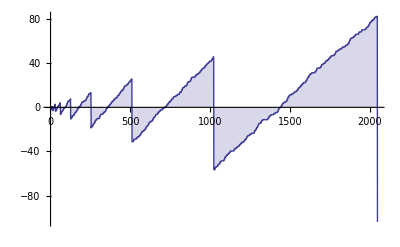

```mathematica
DiscretePlot[ Lin[n],{n,2,64*32}]
```

```mathematica
FG[n_,k_] := Sum[ ((-1)^(j+1))/k-FG[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
FG[100,1]
```

13/10

```mathematica
Lin[100]
```

4/5

Lin[100,1]

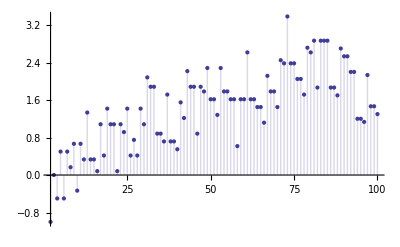

```mathematica
DiscretePlot[FF[n,1],{n,2,100}]
```

```mathematica
Table[ {2^n,lin[2^n],-(2^n - 1)/n},{n,1,14}]//TableForm
```

2 | -1 | -1
4 | -3/2 | -3/2
8 | -7/3 | -7/3
16 | -15/4 | -15/4
32 | -31/5 | -31/5
64 | -21/2 | -21/2
128 | -127/7 | -127/7
256 | -255/8 | -255/8
512 | -511/9 | -511/9
1024 | -1023/10 | -1023/10
2048 | -2047/11 | -2047/11
4096 | -1365/4 | -1365/4
8192 | -8191/13 | -8191/13
16384 | -16383/14 | -16383/14

```mathematica
Table[ {n,ET2[n,1],ET2[n,2],ET2[n,3],ET2[n,4], ET2[n,5], ET2[n,6], ET2[n,7], ET2[n,8], ET2[n,9], ET2[n,10], ET2[n,11], Lin[n]},{n,100,10000,100}]//TableForm
```

100 | -1 | 3 | -4 | -8 | 9 | -5 | 0 | 0 | 0 | 0 | 0 | 4/5
200 | -1 | -1 | -3 | 6 | 24 | -14 | 6 | 0 | 0 | 0 | 0 | 524/105
300 | -1 | 0 | 5 | 3 | -5 | 35 | -22 | 1 | 0 | 0 | 0 | -1711/168
400 | -1 | 5 | -12 | -5 | 5 | -49 | 20 | -7 | 0 | 0 | 0 | 1117/168
500 | -1 | -1 | -3 | -57 | 35 | -1 | 20 | -7 | 0 | 0 | 0 | 3973/168
600 | -1 | -3 | 5 | 17 | 15 | 40 | -64 | 29 | -1 | 0 | 0 | -9389/504
700 | -1 | 1 | 41 | 60 | 70 | -26 | -106 | 21 | -1 | 0 | 0 | -1199/504
800 | -1 | 3 | -9 | 66 | 55 | -40 | 83 | -27 | 8 | 0 | 0 | 5941/504
900 | -1 | 5 | 12 | 56 | 55 | -4 | 118 | -91 | 8 | 0 | 0 | 13753/504
1000 | -1 | -6 | -19 | -16 | 190 | 24 | 20 | -35 | 8 | 0 | 0 | 21061/504
1100 | -1 | -2 | 38 | 110 | -76 | -30 | -134 | 1 | -1 | 1 | 0 | -112171/2520
1200 | -1 | 5 | 14 | -40 | -76 | -36 | -120 | 105 | -37 | 1 | 0 | -81931/2520
1300 | -1 | 3 | 23 | 125 | 134 | 66 | 83 | 127 | -28 | 1 | 0 | -44131/2520
1400 | -1 | 0 | 12 | -83 | -141 | -180 | -36 | 183 | -28 | 1 | 0 | -14311/2520
1500 | -1 | -9 | 9 | -85 | 74 | 180 | 20 | 7 | -28 | 1 | 0 | 28529/2520
1600 | -1 | 13 | 30 | 79 | -161 | -225 | 104 | -125 | 35 | -9 | 0 | 58769/2520
1700 | -1 | -4 | 0 | -13 | -96 | 159 | 412 | -133 | 35 | -9 | 0 | 97829/2520
1800 | -1 | 1 | -13 | 29 | -11 | -69 | 69 | -237 | 128 | -9 | 0 | 128069/2520
1900 | -1 | -10 | -19 | -139 | -281 | -135 | 139 | -237 | 128 | -9 | 0 | 159569/2520
2000 | -1 | 3 | 23 | 29 | 119 | -360 | -155 | -77 | 56 | -9 | 0 | 192329/2520
2100 | -1 | -4 | 35 | 241 | 239 | 345 | -386 | -125 | 11 | 1 | -1 | -2654741/27720
2200 | -1 | 1 | 21 | -9 | -311 | 27 | -14 | 203 | 11 | 1 | -1 | -337763/3960
2300 | -1 | 0 | 114 | 139 | 64 | 261 | -70 | 259 | 11 | 1 | -1 | -276383/3960
2400 | -1 | -1 | -3 | -29 | 129 | 201 | 21 | 267 | -160 | 46 | -1 | -216983/3960
2500 | -1 | 9 | -9 | -116 | 169 | 186 | -42 | 315 | -160 | 46 | -1 | -176393/3960
2600 | -1 | 7 | 21 | 28 | -301 | -420 | -84 | -13 | -223 | 36 | -1 | -132833/3960
2700 | -1 | 4 | 39 | 262 | 354 | 12 | 210 | 203 | -295 | 36 | -1 | -73433/3960
2800 | -1 | 3 | -16 | -150 | 94 | 241 | 343 | 203 | -295 | 36 | -1 | -17993/3960
2900 | -1 | -12 | -73 | -162 | 194 | 187 | -154 | -69 | -34 | 36 | -1 | 31507/3960
3000 | -1 | -3 | -10 | -84 | 364 | 250 | -203 | -49 | -34 | 36 | -1 | 75067/3960
3100 | -1 | -10 | -16 | 218 | -36 | 160 | 511 | -153 | 209 | -44 | 10 | 122587/3960
3200 | -1 | -1 | -85 | -224 | -475 | 181 | 637 | -189 | 173 | -44 | 10 | 162979/3960
3300 | -1 | -8 | 14 | 262 | 220 | -245 | -357 | -413 | 173 | -44 | 10 | 206539/3960
3400 | -1 | 19 | 105 | 140 | 0 | 231 | -63 | -797 | 182 | -44 | 10 | 265939/3960
3500 | -1 | -4 | 66 | 204 | 310 | 69 | -518 | -581 | 362 | -164 | 10 | 311479/3960
3600 | -1 | 13 | 12 | 6 | -235 | -240 | 42 | -265 | 425 | -174 | 10 | 366919/3960
3700 | -1 | -1 | 48 | -90 | -490 | -480 | -42 | -209 | 425 | -174 | 10 | 418399/3960
3800 | -1 | -8 | 36 | 94 | 430 | 816 | 441 | -385 | 425 | -174 | 10 | 467899/3960
3900 | -1 | -1 | 27 | 268 | 670 | 234 | 784 | 407 | 200 | -84 | 10 | 511459/3960
4000 | -1 | 10 | 15 | 108 | 350 | -261 | 462 | 343 | 200 | -84 | 10 | 555019/3960
4100 | -1 | 13 | -10 | -67 | -410 | 231 | -350 | 449 | 287 | -29 | -1 | -736931/3960
4200 | -1 | 5 | 50 | 77 | -505 | -579 | -966 | 505 | 287 | -29 | -1 | -701291/3960
4300 | -1 | -22 | -61 | 151 | 335 | -183 | -1029 | 721 | 215 | -29 | -1 | -637931/3960
4400 | -1 | 7 | 95 | 5 | -345 | 435 | 84 | 161 | -280 | -29 | -1 | -602291/3960
4500 | -1 | 0 | 23 | -19 | 130 | 651 | 147 | 433 | -352 | -29 | -1 | -556751/3960
4600 | -1 | -8 | -19 | -439 | -635 | -195 | -595 | 153 | -352 | -29 | -1 | -509231/3960
4700 | -1 | -17 | -82 | 125 | -70 | -1008 | -560 | 217 | -757 | 231 | -56 | -461711/3960
4800 | -1 | 20 | 80 | 151 | 190 | -288 | -504 | 97 | -505 | 231 | -56 | -414191/3960
4900 | -1 | 15 | 137 | 521 | 1105 | 1110 | 350 | 49 | -496 | 231 | -56 | -382511/3960
5000 | -1 | -3 | -105 | -179 | 465 | 216 | -119 | 321 | -568 | 231 | -56 | -321791/3960
5100 | -1 | -14 | 54 | -67 | -180 | -120 | 1001 | 1161 | -568 | 231 | -56 | -272291/3960
5200 | -1 | 13 | 18 | -125 | -375 | 471 | 1113 | 245 | -199 | 361 | -45 | -228731/3960
5300 | -1 | -5 | 6 | 19 | 300 | 1575 | 1442 | -99 | -199 | 361 | -45 | -189131/3960
5400 | -1 | -2 | -42 | -1 | -340 | -735 | 0 | -259 | -550 | 451 | -45 | -147551/3960
5500 | -1 | 9 | 24 | 133 | 495 | 99 | -84 | -371 | -550 | 451 | -45 | -96071/3960
5600 | -1 | 1 | 48 | 281 | 810 | 195 | -252 | -491 | -550 | 451 | -45 | -44591/3960
5700 | -1 | -16 | -90 | -159 | -505 | -714 | 154 | -371 | -487 | 441 | -45 | 2929/3960
5800 | -1 | 3 | 15 | 73 | 310 | -495 | -777 | 69 | 125 | 81 | -45 | 42529/3960
5900 | -1 | -5 | -28 | -107 | -400 | -1915 | -1848 | -315 | 50 | 81 | -45 | 105889/3960
6000 | -1 | 14 | 110 | 163 | 415 | -751 | -1071 | 21 | 50 | 81 | -45 | 133609/3960
6100 | -1 | 7 | 35 | -171 | 330 | 41 | -385 | -435 | -454 | 81 | -45 | 181129/3960
6200 | -1 | 5 | 53 | 241 | -520 | -109 | -91 | -1155 | 221 | -269 | 54 | 224689/3960
6300 | -1 | -12 | 26 | 413 | 710 | 1631 | 441 | -1387 | 185 | -269 | 54 | 278149/3960
6400 | -1 | 3 | -22 | 145 | 620 | 1595 | 252 | -1435 | 266 | -224 | 54 | 337549/3960
6500 | -1 | -15 | -4 | 53 | -80 | 869 | 1155 | 245 | 896 | -224 | 54 | 369229/3960
6600 | -1 | -6 | 74 | 220 | -385 | -754 | 154 | 462 | 824 | -224 | 54 | 103321/990
6700 | -1 | 4 | 41 | 236 | -335 | -550 | 189 | 134 | 887 | -234 | 54 | 113221/990
6800 | -1 | 3 | -127 | -574 | -815 | -184 | -497 | -378 | 1391 | -234 | 54 | 125101/990
6900 | -1 | -2 | 225 | 502 | 470 | 644 | -49 | -210 | 1391 | -234 | 54 | 68903/495
7000 | -1 | 0 | 33 | -210 | -430 | -520 | -406 | 638 | 1292 | -624 | 219 | 75338/495
7100 | -1 | -3 | 12 | 36 | 555 | 395 | 427 | 1274 | 1220 | -624 | 219 | 79793/495
7200 | -1 | 1 | -66 | -64 | -40 | 629 | 840 | -6 | 707 | -704 | 230 | 84743/495
7300 | -1 | 12 | -36 | -194 | -425 | -31 | 623 | 154 | 635 | -704 | 230 | 90188/495
7400 | -1 | 21 | 21 | -452 | -680 | 443 | 1043 | 154 | 635 | -704 | 230 | 94643/495
7500 | -1 | -1 | -9 | -224 | 75 | 1379 | 1106 | -118 | 896 | -704 | 230 | 100088/495
7600 | -1 | 10 | 153 | 238 | 115 | -811 | -1918 | -1246 | 896 | -704 | 230 | 107513/495
7700 | -1 | 2 | -6 | 502 | 620 | -1525 | -1148 | -902 | 23 | -174 | 120 | 113453/495
7800 | -1 | -1 | 39 | 184 | -296 | -1882 | -644 | -986 | -607 | -426 | 120 | 118403/495
7900 | -1 | -3 | -12 | 72 | -81 | -1576 | -707 | -1106 | -607 | -426 | 120 | 123353/495
8000 | -1 | 0 | -34 | -64 | -596 | -1966 | 28 | -370 | -514 | -426 | 120 | 257101/990
8100 | -1 | 3 | 80 | 610 | 1914 | 599 | 532 | 490 | 98 | -786 | 120 | 267991/990
8200 | -1 | -17 | -172 | -194 | -36 | 1271 | -196 | 946 | -397 | -566 | 54 | -4496507/12870
8300 | -1 | -4 | -4 | -332 | -1091 | -91 | -504 | 1282 | -397 | -566 | 54 | -4316327/12870
8400 | -1 | 0 | 35 | -216 | -781 | 665 | 966 | 2170 | -469 | -566 | 54 | -4200497/12870
8500 | -1 | 1 | 35 | 184 | -231 | -316 | 252 | 2290 | -820 | -476 | 54 | -4097537/12870
8600 | -1 | 1 | 65 | 376 | 19 | -784 | -252 | 2338 | -820 | -476 | 54 | -3943097/12870
8700 | -1 | -20 | -64 | -374 | -176 | 680 | -588 | 378 | -568 | 364 | 54 | -3775787/12870
8800 | -1 | 12 | 20 | -382 | -216 | 1694 | 154 | -70 | -469 | 354 | 54 | -3634217/12870
8900 | -1 | 3 | 104 | 380 | 1659 | 3200 | 728 | 146 | -541 | 354 | 54 | -3466907/12870
9000 | -1 | 7 | -43 | -208 | 324 | 800 | -763 | -182 | -892 | 444 | 54 | -3351077/12870
9100 | -1 | 12 | 92 | 30 | -116 | -4 | 133 | 1546 | -262 | 444 | 54 | -3209507/12870
9200 | -1 | -2 | 74 | 54 | 1144 | 2000 | 581 | 1266 | -262 | 444 | 54 | -3055067/12870
9300 | -1 | 3 | 21 | 624 | 674 | -266 | 595 | 770 | -775 | 1219 | -320 | -2913497/12870
9400 | -1 | -17 | 105 | 896 | 529 | -236 | 1848 | 1602 | -775 | 1219 | -320 | -2771927/12870
9500 | -1 | -16 | -90 | -204 | -1191 | -1454 | 1036 | 1330 | -514 | 1219 | -320 | -1286221/6435
9600 | -1 | 18 | -102 | -568 | -1081 | -1154 | 399 | 1266 | -406 | 859 | -320 | -1241176/6435
9700 | -1 | -1 | 45 | -116 | -381 | -605 | 532 | 1266 | -406 | 859 | -320 | -1157521/6435
9800 | -1 | 3 | -3 | -412 | -1481 | -2885 | -2912 | -1190 | -595 | 849 | -320 | -1086736/6435
9900 | -1 | -16 | -27 | 444 | 1399 | -56 | -1827 | -974 | -667 | 849 | -320 | -1009516/6435
10000 | -1 | 5 | -6 | 411 | 1139 | -794 | -1253 | -168 | -1018 | 939 | -320 | -951601/6435

```mathematica
LAdd[n_] := Sum[ 2^k/k,{k,1,Log[2,n]}]
```

```mathematica
N[Lin[1000]+LAdd[1000]]
```

176.696

```mathematica
N[Sum[ MangoldtLambda[n]/Log[n],{n,2,1000}]]
```

176.696

```mathematica
Expand[(2^k - 1)/k + 1/k]
```

2^k/k

```mathematica
Expand[Sum[ 2^k/k,{k,1,Log[2,n]}]]
```

-ⅈ π-2 n LerchPhi[2,1,1+Log[n]/Log[2]]

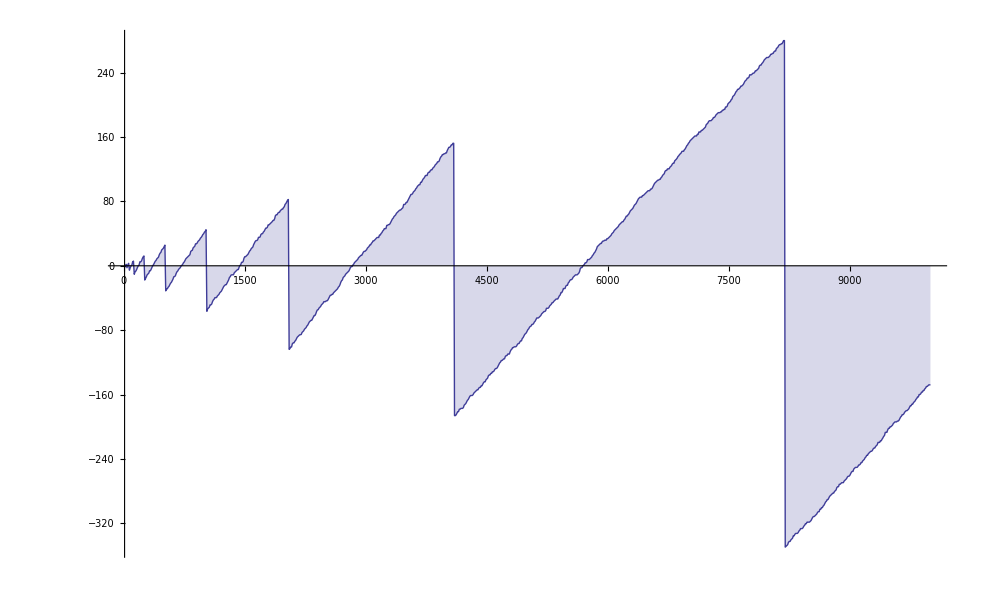

```mathematica
DiscretePlot[ Lin[n],{n,10,10000,10}]
```

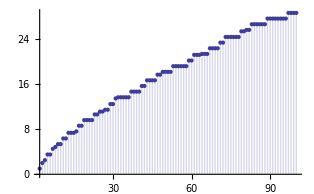

```mathematica
DiscretePlot[ Lin[n]+LAdd[n],{n,2,100}]
```

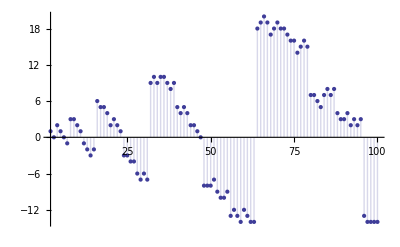

```mathematica
DiscretePlot[ MLin[n],{n,2,100}]
```

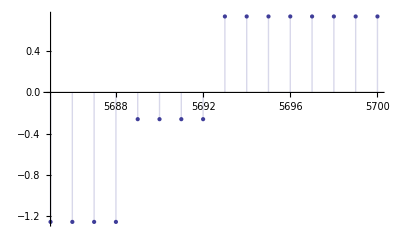

```mathematica
DiscretePlot[ Lin[n],{n,5685,5700}]
```

```mathematica
N[Lin[5693]]
```

0.739646

```mathematica
N[(5693-4096)/4096]
```

0.389893

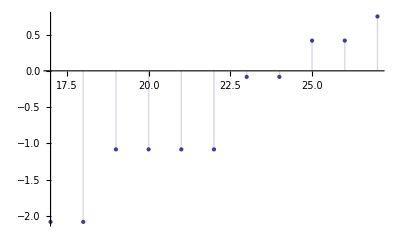

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^4)*1.1],Floor[(2^4)*1.7]}]
```

```mathematica
Lin[24]
```

-1/12

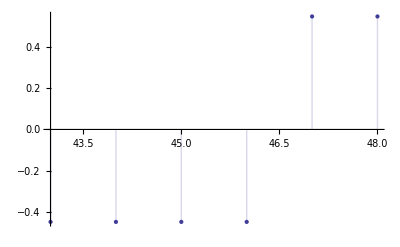

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^5)*1.37],Floor[(2^5)*1.52]}]
```

```mathematica
Lin[46]
```

-9/20

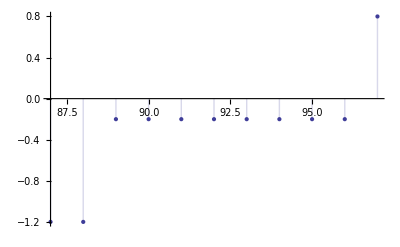

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^6)*1.37],Floor[(2^6)*1.52]}]
```

```mathematica
Lin[ 96]
```

-1/5

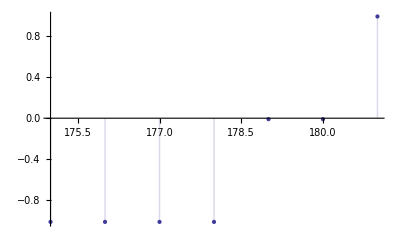

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^7)*1.37],Floor[(2^7)*1.42]}]
```

```mathematica
Lin[ 180]
```

-1/105

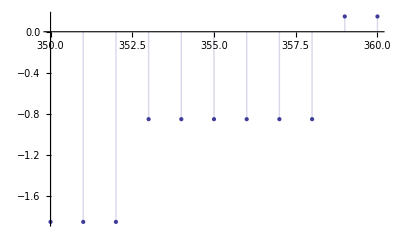

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^8)*1.37],Floor[(2^8)*1.41]}]
```

```mathematica
Lin[358]
```

-143/168

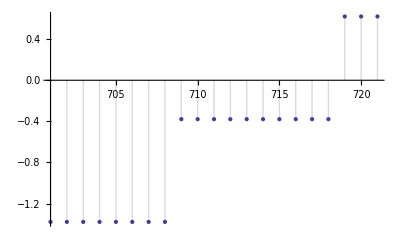

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^9)*1.37],Floor[(2^9)*1.41]}]
```

```mathematica
N[Lin[ 718]]
```

-0.378968

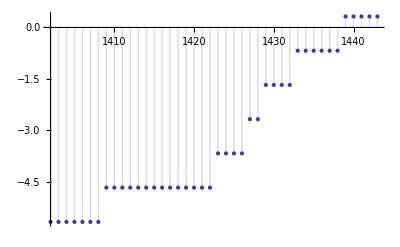

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^10)*1.37],Floor[(2^10)*1.41]}]
```

```mathematica
N[Lin[ 1438]]
```

-0.678968

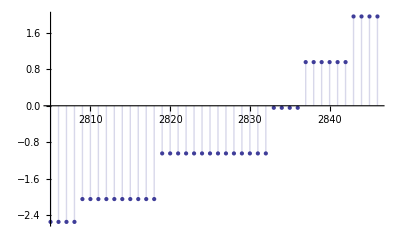

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^11)*1.37],Floor[(2^11)*1.39]}]
```

```mathematica
N[Lin[ 2836]]
```

-0.0436869

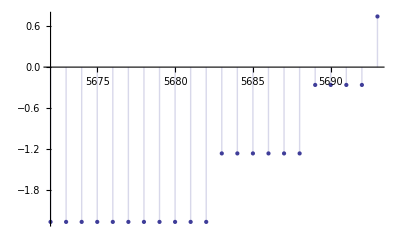

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^12)*1.385],Floor[(2^12)*1.39]}]
```

```mathematica
N[Lin[ 5692]]
```

-0.260354

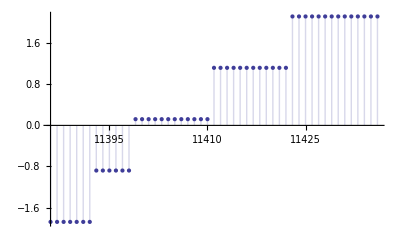

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^13)*1.39],Floor[(2^13)*1.396]}]
```

```mathematica
N[Lin[11398]]
```

-0.878943

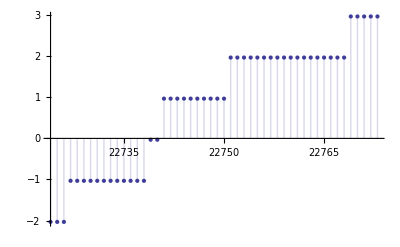

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^14)*1.387],Floor[(2^14)*1.39]}]
```

```mathematica
N[Lin[22740]]
```

-0.0321179

```mathematica
DiscretePlot[ Lin[n],{n,Floor[ (2^15)*1.385],Floor[(2^15)*1.4]}]
```

$Aborted

```mathematica
dif:={24, 46, 96, 180, 358, 718, 1438, 2836, 5692, 11398, 22740}
N[Table[ {j, dif[[j]],dif[[j]]/(2^(j+3.5)),dif[[j+1]]/dif[[j]]},{j,1,Length[dif]-1}]//TableForm]
```

1. | 24. | 1.06066 | 1.91667
2. | 46. | 1.01647 | 2.08696
3. | 96. | 1.06066 | 1.875
4. | 180. | 0.994369 | 1.98889
5. | 358. | 0.988845 | 2.00559
6. | 718. | 0.991607 | 2.00279
7. | 1438. | 0.992988 | 1.97218
8. | 2836. | 0.979177 | 2.00705
9. | 5692. | 0.98263 | 2.00246
10. | 11398. | 0.983838 | 1.99509

```mathematica
aba=Floor[2^(19+(1/2))]*.983
N[LAdd[  aba]]
N[LogIntegral[aba]]
N[PP[aba]]
```

728850.

58713.6

58785.

58784.9

```mathematica
PP[n_] := N[Sum[ 1/k PrimePi[ n^(1/k)],{k,1,n}]]
```

```mathematica
PP[10000]
```

1247.1

```mathematica
N[Table[2^(j+1/2),{j,2,18}]]
```

{5.65685,11.3137,22.6274,45.2548,90.5097,181.019,362.039,724.077,1448.15,2896.31,5792.62,11585.2,23170.5,46341.,92681.9,185364.,370728.}

```mathematica
LI1[n_] := Sum[ 2^k/k,{k,1,Log[2,n]}]
```

```mathematica
LI1[n]
```

-ⅈ (π-2 ⅈ n LerchPhi[2,1,1+Log[n]/Log[2]])

```mathematica
LI2[n_] := Integrate[ 2^k/k,{k,1,Log[2,n]}]
```

```mathematica
LI2[n]
```

ConditionalExpression[Log[Log[2]]-Log[Log[n]]-LogIntegral[2]+LogIntegral[n],Im[Log[n]]≠0||Re[Log[n]]≥0]

```mathematica
Integrate[ 2^k/k,{k,1,Log[2,n]}]
```

ConditionalExpression[Log[Log[2]]-Log[Log[n]]-LogIntegral[2]+LogIntegral[n],Im[Log[n]]≠0||Re[Log[n]]≥0]

```mathematica
Integrate[ 3^k/k,{k,1,Log[3,n]}]
```

ConditionalExpression[Log[Log[3]]-Log[Log[n]]-LogIntegral[3]+LogIntegral[n],Im[Log[n]]≠0||Re[Log[n]]≥0]

Power::infy: Infinite expression 1/0 encountered.

```mathematica
Integrate[ 2^k/k,{k,1,Log[2,n]}]
```

ConditionalExpression[Log[Log[2]]-Log[Log[n]]-LogIntegral[2]+LogIntegral[n],Im[Log[n]]≠0||Re[Log[n]]≥0]

```mathematica
tt[n_] := Log[Log[2]]-Log[Log[n]]-LogIntegral[2]+LogIntegral[n]
```

```mathematica
N[tt[10000]]
```

1242.51

```mathematica
N[LogIntegral[10000]]
```

1246.14

```mathematica
N[LI1[10000]]
```

1394.98

LogIntegral[100]

```mathematica
LAdd[n_, v_] := Sum[ v^k/k,{k,1,Log[v,n]}]
```

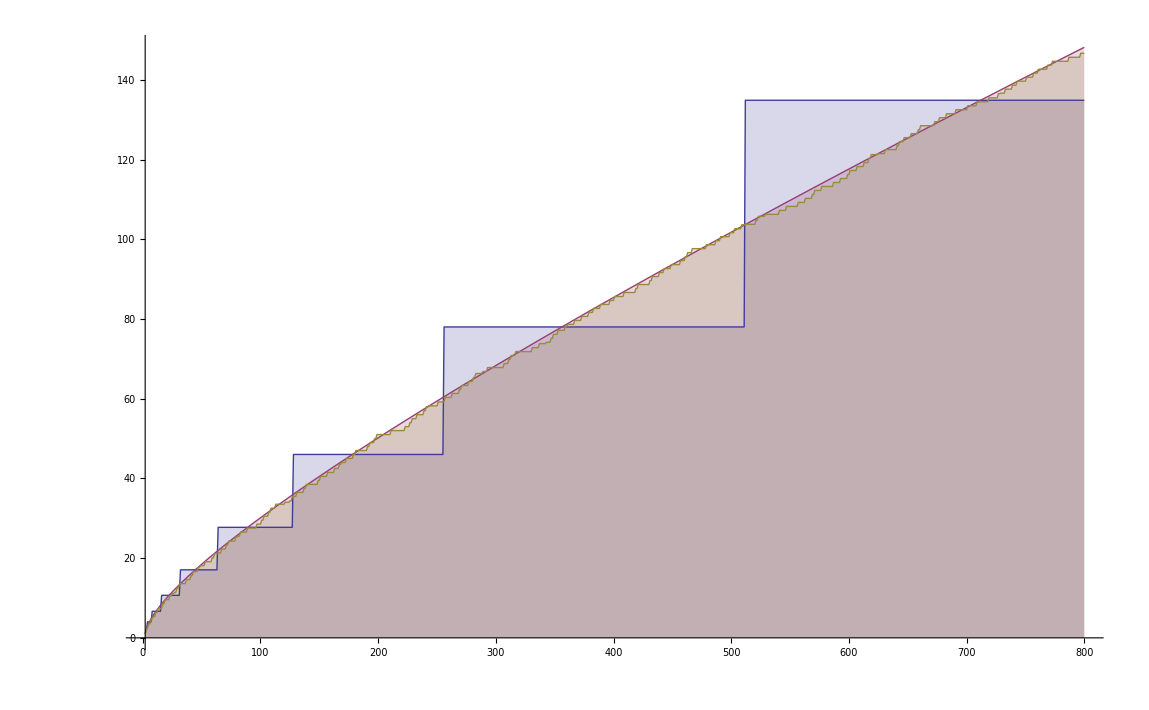

```mathematica
DiscretePlot[ { LAdd[n], LogIntegral[n], PP[n]},{n,2,800}]
```

```mathematica
Integrate[ 3^k/k,{k,1,Log[3,n]}]
```

ConditionalExpression[Log[Log[3]]-Log[Log[n]]-LogIntegral[3]+LogIntegral[n],Im[Log[n]]≠0||Re[Log[n]]≥0]

```mathematica
Integrate[ 8^k/k,{k,1,Log[8,n]}]
```

ConditionalExpression[Log[Log[8]]-Log[Log[n]]-LogIntegral[8]+LogIntegral[n],Im[Log[n]]≠0||Re[Log[n]]≥0]

```mathematica
Integrate[ (1.5)^k/k,{k,1,Log[(1.5),n]}]
```

ConditionalExpression[(-1.02779+0. ⅈ)-1. Gamma[0,-1. Log[n]]-1. Log[-1. Log[n]],Im[Log[n]]≠0||Re[Log[n]]≥0]

```mathematica
LAdd[n_,k_] := Sum[ k^j/j,{j,1,Log[k,n]}]
Table[ { n, LAdd[n,1.00001]-LAdd[2,1.00001]+LogIntegral[2], N[LogIntegral[n]]},{n,10,2000,10}]//TableForm
```

10 | 6.16558 | 6.1656
20 | 9.90527 | 9.9053
30 | 13.0226 | 13.0226
40 | 15.8395 | 15.8395
50 | 18.4687 | 18.4687
60 | 20.9654 | 20.9654
70 | 23.3618 | 23.3618
80 | 25.6785 | 25.6786
90 | 27.9299 | 27.9299
100 | 30.1262 | 30.1261
110 | 32.2751 | 32.2751
120 | 34.3828 | 34.3828
130 | 36.454 | 36.4541
140 | 38.4928 | 38.4928
150 | 40.5024 | 40.5023
160 | 42.485 | 42.4852
170 | 44.4438 | 44.4438
180 | 46.3801 | 46.38
190 | 48.2958 | 48.2957
200 | 50.1922 | 50.1922
210 | 52.0709 | 52.0709
220 | 53.9329 | 53.9329
230 | 55.7792 | 55.7793
240 | 57.6109 | 57.6109
250 | 59.4286 | 59.4287
260 | 61.2332 | 61.2334
270 | 63.0254 | 63.0256
280 | 64.8059 | 64.806
290 | 66.575 | 66.5752
300 | 68.3338 | 68.3336
310 | 70.082 | 70.0818
320 | 71.8199 | 71.8202
330 | 73.5493 | 73.5491
340 | 75.2691 | 75.2691
350 | 76.9805 | 76.9804
360 | 78.6835 | 78.6834
370 | 80.3785 | 80.3783
380 | 82.0658 | 82.0656
390 | 83.7452 | 83.7453
400 | 85.4179 | 85.4179
410 | 87.0833 | 87.0835
420 | 88.7423 | 88.7423
430 | 90.3946 | 90.3947
440 | 92.0407 | 92.0407
450 | 93.6803 | 93.6805
460 | 95.3143 | 95.3145
470 | 96.9427 | 96.9426
480 | 98.5649 | 98.5651
490 | 100.182 | 100.182
500 | 101.794 | 101.794
510 | 103.401 | 103.4
520 | 105.002 | 105.002
530 | 106.598 | 106.599
540 | 108.191 | 108.19
550 | 109.777 | 109.777
560 | 111.36 | 111.36
570 | 112.938 | 112.938
580 | 114.511 | 114.512
590 | 116.081 | 116.081
600 | 117.647 | 117.647
610 | 119.208 | 119.208
620 | 120.765 | 120.765
630 | 122.319 | 122.318
640 | 123.868 | 123.868
650 | 125.414 | 125.414
660 | 126.956 | 126.956
670 | 128.495 | 128.494
680 | 130.029 | 130.029
690 | 131.561 | 131.561
700 | 133.089 | 133.089
710 | 134.613 | 134.614
720 | 136.135 | 136.135
730 | 137.653 | 137.654
740 | 139.169 | 139.169
750 | 140.681 | 140.681
760 | 142.19 | 142.19
770 | 143.696 | 143.696
780 | 145.199 | 145.199
790 | 146.699 | 146.699
800 | 148.197 | 148.197
810 | 149.691 | 149.691
820 | 151.183 | 151.183
830 | 152.672 | 152.672
840 | 154.159 | 154.159
850 | 155.643 | 155.642
860 | 157.124 | 157.124
870 | 158.602 | 158.602
880 | 160.078 | 160.079
890 | 161.552 | 161.552
900 | 163.023 | 163.024
910 | 164.492 | 164.492
920 | 165.959 | 165.959
930 | 167.423 | 167.423
940 | 168.885 | 168.885
950 | 170.344 | 170.345
960 | 171.802 | 171.802
970 | 173.258 | 173.257
980 | 174.71 | 174.71
990 | 176.16 | 176.161
1000 | 177.609 | 177.61
1010 | 179.057 | 179.056
1020 | 180.501 | 180.501
1030 | 181.943 | 181.943
1040 | 183.384 | 183.384
1050 | 184.823 | 184.822
1060 | 186.258 | 186.259
1070 | 187.693 | 187.693
1080 | 189.127 | 189.126
1090 | 190.556 | 190.557
1100 | 191.986 | 191.986
1110 | 193.413 | 193.413
1120 | 194.837 | 194.838
1130 | 196.261 | 196.261
1140 | 197.682 | 197.683
1150 | 199.103 | 199.103
1160 | 200.521 | 200.521
1170 | 201.937 | 201.937
1180 | 203.352 | 203.352
1190 | 204.765 | 204.765
1200 | 206.176 | 206.176
1210 | 207.586 | 207.585
1220 | 208.994 | 208.993
1230 | 210.4 | 210.4
1240 | 211.805 | 211.804
1250 | 213.208 | 213.208
1260 | 214.61 | 214.609
1270 | 216.009 | 216.009
1280 | 217.408 | 217.408
1290 | 218.805 | 218.805
1300 | 220.2 | 220.2
1310 | 221.593 | 221.594
1320 | 222.987 | 222.986
1330 | 224.378 | 224.377
1340 | 225.768 | 225.767
1350 | 227.155 | 227.155
1360 | 228.541 | 228.542
1370 | 229.927 | 229.927
1380 | 231.311 | 231.311
1390 | 232.693 | 232.693
1400 | 234.075 | 234.074
1410 | 235.455 | 235.454
1420 | 236.832 | 236.832
1430 | 238.209 | 238.209
1440 | 239.585 | 239.585
1450 | 240.96 | 240.96
1460 | 242.332 | 242.333
1470 | 243.705 | 243.704
1480 | 245.075 | 245.075
1490 | 246.444 | 246.444
1500 | 247.812 | 247.812
1510 | 249.18 | 249.179
1520 | 250.545 | 250.545
1530 | 251.908 | 251.909
1540 | 253.272 | 253.272
1550 | 254.633 | 254.634
1560 | 255.994 | 255.995
1570 | 257.353 | 257.354
1580 | 258.712 | 258.712
1590 | 260.069 | 260.07
1600 | 261.425 | 261.426
1610 | 262.78 | 262.78
1620 | 264.133 | 264.134
1630 | 265.487 | 265.487
1640 | 266.837 | 266.838
1650 | 268.188 | 268.189
1660 | 269.537 | 269.538
1670 | 270.886 | 270.886
1680 | 272.233 | 272.233
1690 | 273.58 | 273.579
1700 | 274.925 | 274.924
1710 | 276.267 | 276.268
1720 | 277.61 | 277.61
1730 | 278.952 | 278.952
1740 | 280.292 | 280.293
1750 | 281.632 | 281.633
1760 | 282.971 | 282.971
1770 | 284.31 | 284.309
1780 | 285.645 | 285.646
1790 | 286.98 | 286.981
1800 | 288.315 | 288.316
1810 | 289.648 | 289.649
1820 | 290.981 | 290.982
1830 | 292.313 | 292.314
1840 | 293.644 | 293.644
1850 | 294.973 | 294.974
1860 | 296.302 | 296.303
1870 | 297.632 | 297.631
1880 | 298.958 | 298.958
1890 | 300.282 | 300.284
1900 | 301.608 | 301.609
1910 | 302.932 | 302.933
1920 | 304.255 | 304.256
1930 | 305.579 | 305.578
1940 | 306.901 | 306.9
1950 | 308.221 | 308.22
1960 | 309.539 | 309.54
1970 | 310.858 | 310.858
1980 | 312.178 | 312.176
1990 | 313.492 | 313.493
2000 | 314.81 | 314.809

```mathematica
Limit[ Sum[ v^k/k,{k,1,Log[v,n]}],{v->1}]
```

{Limit[-n v LerchPhi[v,1,1+Log[n]/Log[v]]-Log[1-v],v→1]}

```mathematica
Sum[ v^k/k,{k,1,Log[v,n]}]
```

```mathematica
LAdd[n_, v_] := Sum[ v^k/k,{k,1,Log[v,n]}]
```

```mathematica
LAdd[80,1.000001]-LAdd[2,1.000001]+N[LogIntegral[2]]
```

25.6786-2.49006×10^-10 ⅈ

```mathematica
N[LogIntegral[80]]
```

25.6786

```mathematica
LAdd[ 2,1.00000001]
```

19.4658+1.01851×10^-8 ⅈ

```mathematica
N[LogIntegral[2]]
```

1.04516

```mathematica
LAdd[ 2,1-.000001]
```

0

```mathematica
LAdd2[n_, v_] := Sum[ (-1)^(k+1) v^k/k,{k,1,Log[v,n]}]
```

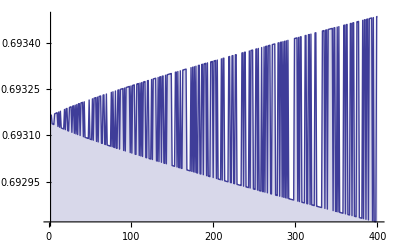

```mathematica
DiscretePlot[ { LAdd2[n,1.00001]},{n,2,400}]
```

```mathematica
N[Log[2]]
```

0.693147

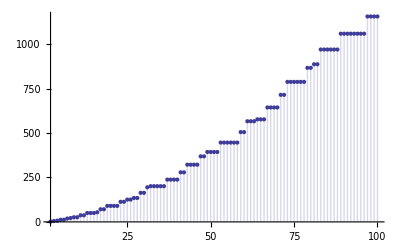

```mathematica
LAdd[n_,k_] := Sum[ k^j/j,{j,1,Log[k,n]}]
L2[n_] := Sum[ LAdd[n, Prime[k]],{k,1,200}]
DiscretePlot[L2[n],{n,2,100}]
```

```mathematica
PX[n_,k_] := PX[n,k]=Sum[ j(1/k-PX[Floor[n/j],k+1]),{j,2,n}]
```

```mathematica
PX[100,1]
```

69389/60

```mathematica
L2[100]
```

69389/60

```mathematica
DiscretePlot[ PX[n,1],{n,2,100}]
```

-Graphics-

```mathematica
Integrate[ k^j/j,{j,1,Log[k,n]}]
```

ConditionalExpression[-LogIntegral[k]+LogIntegral[n],Log[n]<Log[k]<0]

```mathematica
Integrate[ k^j/j,{j,1,n}]
```

ConditionalExpression[ExpIntegralEi[n Log[k]]-LogIntegral[k],Re[Log[k]]<0&&n>1]

Integrate::idiv: Integral of k^j/j does not converge on {0, Log[n]/Log[k]}.

```mathematica
LAddX[n_,k_] := Integrate[ k^j/j,{j,1,Log[k,n]}]
L2X[n_] := Sum[ LAddX[n, Prime[k]],{k,1,200}]
DiscretePlot[L2X[n],{n,2,100}]
```

$Aborted

```mathematica
LAddX[n_,k_] := Sum[ k^j/j,{j,1,Log[k,n]}]
L2X[n_] := Sum[ LAddX[n, Prime[k]],{k,1,200}]
DiscretePlot[L2X[n],{n,2,100}]
```

-Graphics-

```mathematica
Integrate[2^j/j,{j,1,Log[2,100]}]
```

-ExpIntegralEi[Log[2]]+ExpIntegralEi[Log[100]]

```mathematica
N[-ExpIntegralEi[Log[2]]+ExpIntegralEi[Log[100]]]
```

29.081

```mathematica
N[LogIntegral[100]-LogIntegral[2]]
```

29.081

```mathematica
Soldner := 1.4513692348
lt[n_,k_] := Sum[ k^j/j,{j,Log[k,Soldner],Log[k,n]}]
Table[ { n, lt[n,1.00001], N[LogIntegral[n]]},{n,120,123}]//TableForm
```

120 | 34.3828 | 34.3828
121 | 34.5915 | 34.5915
122 | 34.7998 | 34.7998
123 | 35.0077 | 35.0078

```mathematica
Integrate[ k^j/j,{j,1,Log[k,n]}]
```

ConditionalExpression[-LogIntegral[k]+LogIntegral[n],Log[n]<Log[k]<0]

```mathematica
-LogIntegral[1.45136923488]+LogIntegral[n]
```

9.07639×10^-12+LogIntegral[n]

```mathematica
Integrate[ Soldner^j/j,{j,1,Log[Soldner,100]}]
```

30.1261-1.15463×10^-14 ⅈ

```mathematica
N[LogIntegral[100]]
```

30.1261

```mathematica
Integrate[ Soldner^j/j,{j,Log[Soldner,50],Log[Soldner,100]}]
```

11.6574-5.77316×10^-15 ⅈ

```mathematica
N[LogIntegral[100]-LogIntegral[50]]
```

11.6574

```mathematica
lt2[n_,b_,k_] := Sum[ k^j/j,{j,Log[k,b],Log[k,n]}]
Table[ { n, lt2[n,2,1.00001], N[LogIntegral[n]-LogIntegral[2]]},{n,120,123}]//TableForm
```

120 | 33.3377 | 33.3376
121 | 33.5464 | 33.5463
122 | 33.7547 | 33.7547
123 | 33.9626 | 33.9627

```mathematica
N[LogIntegral[30]]
```

13.0226

```mathematica
N[ExpIntegralEi[Log[30]]]
```

13.0226

```mathematica
Expand[Log[a,E^x]]
```

```mathematica
x/Log[a]
```

x/Log[a]

```mathematica
Soldner := 1.4513692348
lt3[n_,k_] := Sum[ k^j/j,{j,Log[k,Soldner],n/Log[k]}]
Table[ { n, lt3[n,1.00001], N[ExpIntegralEi[n]]},{n,4,6,.3}]//TableForm
```

4. | 19.631 | 19.6309
4.3 | 24.2274 | 24.2274
4.6 | 30.0141 | 30.0141
4.9 | 37.3325 | 37.3325
5.2 | 46.6248 | 46.6249
5.5 | 58.4654 | 58.4655
5.8 | 73.6005 | 73.6008

```mathematica
ff[x_] := Log[ⅇ^x]
```

```mathematica
ff[3]
```

3

```mathematica
Integrate[ Soldner^j/j,{j,1,12/Log[Soldner]}]
```

14959.5-1.99307×10^-11 ⅈ

```mathematica
N[ExpIntegralEi[12]]
```

14959.5

```mathematica
Integrate[ a^j/j,{j,1,Log[a,n]}]
```

ConditionalExpression[-LogIntegral[a]+LogIntegral[n],Log[n]<Log[a]<0]

```mathematica
N[Integrate[ E^j/j,{j,1,Log[E,100]}]]
```

28.231

```mathematica
N[LogIntegral[100]-LogIntegral[E]]
```

28.231

```mathematica
N[Integrate[ E^j/j,{j,1,Log[1000]}]]
N[LogIntegral[1000]-LogIntegral[E]]
```

175.715

175.715

```mathematica
Integrate[ E^j/j,{j,1,n}]
```

ConditionalExpression[CoshIntegral[n]-ExpIntegralEi[1]-Log[n]+SinhIntegral[n],Im[n]≠0||Re[n]≥0]

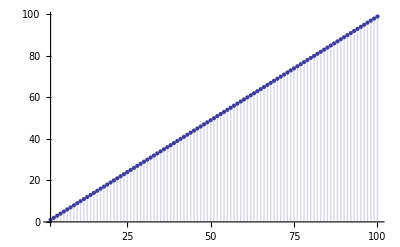

```mathematica
LAdd2a[n_, v_] := Sum[ v^k,{k,1,Log[v,n]}]
DiscretePlot[ { LAdd2a[n,1+.000001]*.000001},{n,2,100}]
```

```mathematica
LAdd2a[100,1.0000001]
```

9.9×10^8

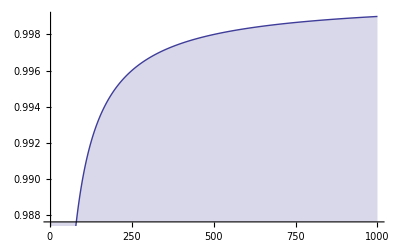

```mathematica
LAdd2a[n_, v_] := Sum[ v^(-k),{k,1,Log[v,n]}]
DiscretePlot[ { LAdd2a[n,1+.000001]*.000001},{n,2,1000}]
```

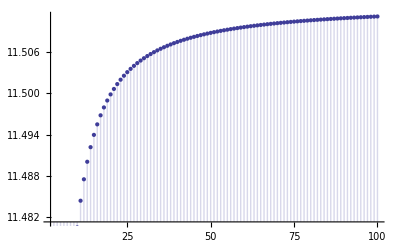

```mathematica
LAdd2a[n_, v_] := Sum[ v^(-k)/k,{k,1,Log[v,n]}]
DiscretePlot[ { LAdd2a[n,1+.00001]},{n,2,100}]
```